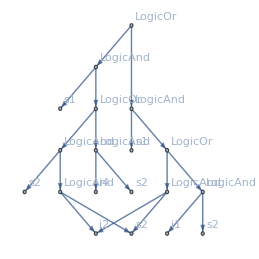
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Func[LogicAnd],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],18→Term[i2],19→Term[s2],19→Term[s2]}}

```mathematica
{vertex1,vertex2} = RandomSample[Drop[VertexList[g1],1],2];
cropped = DeleteSubtree[g1,l1,vertex1];
sub = Subtree[g1,l1,vertex2];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
```

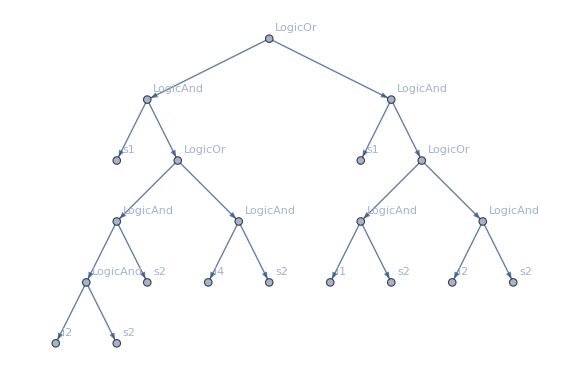
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Func[LogicAnd],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2],20→Term[i2],21→Term[s2]}}

```mathematica
InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
```

```mathematica
{vertex1,vertex2}
```

{6,17}

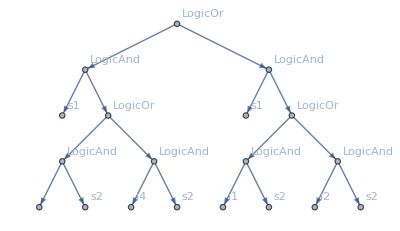
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
cropped
```

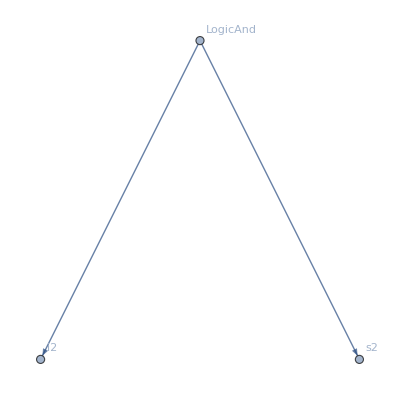
{-Graphics-,{17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
sub
```

```mathematica
Cases[l1[[All,2]],_Term]
```

{Term[s1],Term[i3],Term[s2],Term[i4],Term[s2],Term[s1],Term[i1],Term[s2],Term[i2],Term[s2]}

```mathematica
terminalSet = {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]}
```

{Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]}

```mathematica
lab = {1->Func[LogicOr],2->Func[LogicAnd],3->Term[s1],4->Func[LogicOr],5->Func[LogicAnd],6->Term[i3],7->Term[s2],8->Func[LogicAnd],9->Term[i4],10->Term[s2],11->Func[LogicAnd],12->Term[s1],13->Func[LogicOr],14->Func[LogicAnd],15->Term[i1],16->Term[s1],17->Func[LogicAnd],18->Term[i2],19->Term[s2]}
```

{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s1],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}

```mathematica
replacePos = RandomChoice[Cases[lab,(x_->_Term):>x]]
```

10

```mathematica
availableTerminals = Complement[terminalSet,Cases[lab,(replacePos->t_):>t]]
```

{Term[i1],Term[i2],Term[i3],Term[i4],Term[s1]}

```mathematica
ReplaceAll[lab, (replacePos->_)->(replacePos->RandomChoice[availableTerminals])]
```

{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s1],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s1],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}

```mathematica
Map[Func,DeleteDuplicates@Cases[lab,(x_->Func[y_]):>y]]
```

{Func[LogicOr],Func[LogicAnd]}

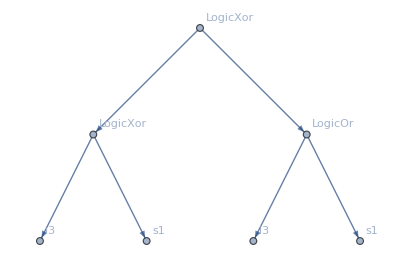
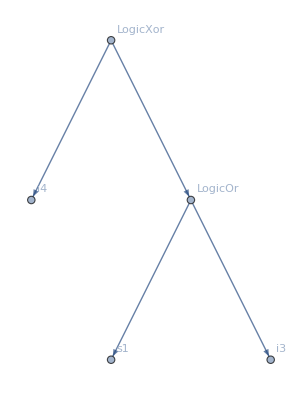
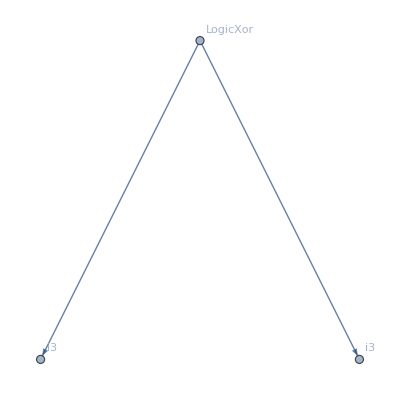
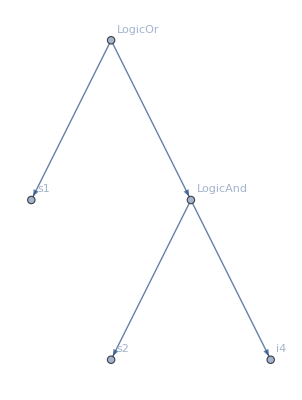
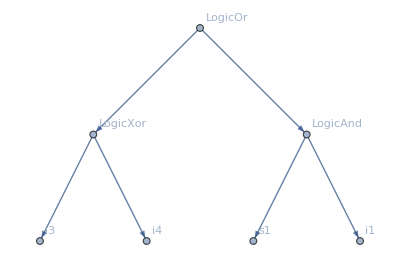
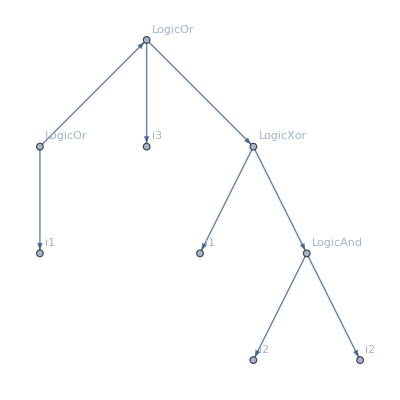
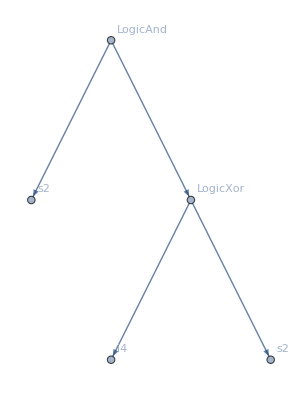
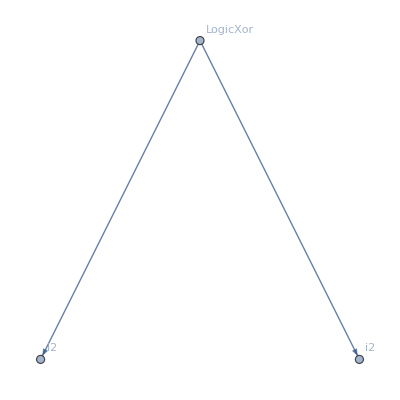
{{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i3],5→Term[s1],6→Term[i3],7→Term[s1]}},{-Graphics-,{1→Func[LogicXor],2→Term[i4],3→Func[LogicOr],4→Term[s1],5→Term[i3]}},{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Func[LogicOr],4→Term[i3],5→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Func[LogicAnd],4→Term[s1],5→Term[i1],6→Term[i3],7→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[i1],4→Term[i3],5→Func[LogicXor],6→Term[i1],7→Func[LogicAnd],8→Term[i2],9→Term[i2]}},{-Graphics-,{1→Func[LogicAnd],2→Term[s2],3→Func[LogicXor],4→Term[i4],5→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Term[i2]}},{-Graphics-,{1→Func[LogicAnd],2→Func[LogicOr],3→Term[i3],4→Term[i4],5→Term[s1]}},{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicAnd],4→Func[LogicOr],5→Func[LogicXor],6→Term[s1],7→Term[i1],8→Term[i3],9→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[s2],4→Term[i2],5→Func[LogicAnd],6→Term[i2],7→Term[i2]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Func[LogicAnd],4→Term[i2],5→Term[s1],6→Func[LogicAnd],7→Term[i4],8→Term[i4],9→Term[s1]}},{-Graphics-,{1→Func[LogicAnd],2→Term[s2],3→Term[i2]}},{-Graphics-,{1→Func[LogicOr],2→Term[s2],3→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Term[s2],3→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Func[LogicAnd],4→Term[i3],5→Term[s2],6→Term[i3],7→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Term[s2],3→Term[i2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Func[LogicOr],4→Term[i2],5→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[i2],4→Term[i4],5→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Term[i2],5→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Term[s2],4→Term[i4],5→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Func[LogicOr],4→Term[i1],5→Func[LogicAnd],6→Term[i3],7→Term[i4]}},{-Graphics-,{1→Func[LogicAnd],2→Func[LogicOr],3→Term[i3],4→Term[s2],5→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Func[LogicOr],4→Func[LogicOr],5→Term[i3],6→Term[i2],7→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[i4],4→Term[i3],5→Term[i3]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i1],3→Func[LogicAnd],4→Term[s1],5→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Term[i2],4→Term[s2],5→Term[i3]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i4],3→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Func[LogicXor],4→Term[s1],5→Func[LogicXor],6→Term[s1],7→Term[i2]}},{-Graphics-,{1→Func[LogicXor],2→Term[i1],3→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Term[i4],3→Func[LogicOr],4→Term[i1],5→Func[LogicAnd],6→Term[i4],7→Func[LogicAnd],8→Term[s1],9→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[s2],4→Term[s2],5→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Term[i3]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i2],3→Term[i4]}},{-Graphics-,{1→Func[LogicXor],2→Func[LogicAnd],3→Func[LogicAnd],4→Term[i1],5→Term[s2],6→Func[LogicAnd],7→Term[i2],8→Term[i2],9→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[i4],4→Term[s2],5→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Func[LogicOr],4→Term[i1],5→Func[LogicXor],6→Term[s1],7→Term[i2],8→Term[s2],9→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicXor],6→Func[LogicXor],7→Term[i2],8→Term[i2],9→Term[i4],10→Term[i2],11→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Term[i2]}},{-Graphics-,{1→Func[LogicXor],2→Term[s2],3→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Func[LogicOr],4→Term[i3],5→Term[i1]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i3],3→Term[s2]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i3],3→Term[i3]}},{-Graphics-,{1→Func[LogicXor],2→Term[i4],3→Term[i2]}},{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Term[i2]}},{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicXor],4→Term[i3],5→Term[s1],6→Term[i3],7→Func[LogicXor],8→Term[i1],9→Term[s1]}},{-Graphics-,{1→Func[LogicXor],2→Term[i4],3→Func[LogicOr],4→Term[s1],5→Term[s2]}},{-Graphics-,{1→Func[LogicAnd],2→Func[LogicXor],3→Term[i3],4→Term[i2],5→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Func[LogicAnd],4→Func[LogicOr],5→Term[i4],6→Term[s2],7→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Func[LogicOr],4→Term[s1],5→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[i2],4→Term[i3],5→Term[i2]}},{-Graphics-,{1→Func[LogicAnd],2→Term[s2],3→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Term[s2],4→Term[i1],5→Term[i2]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i4],3→Term[s1]}},{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[s2],4→Func[LogicXor],5→Func[LogicAnd],6→Term[i2],7→Term[i1],8→Term[i3],9→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Func[LogicAnd],4→Term[i2],5→Term[i4],6→Term[i2],7→Term[i4]}},{-Graphics-,{1→Func[LogicXor],2→Term[s2],3→Term[i4]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i2],3→Func[LogicAnd],4→Term[i1],5→Term[i3]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i4],3→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Term[s2],3→Func[LogicAnd],4→Term[i3],5→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Func[LogicOr],3→Term[i2],4→Term[i1],5→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Term[i1]}},{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Term[i2]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s2],4→Term[i4],5→Term[i3]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[s1],4→Term[i4],5→Func[LogicOr],6→Term[i2],7→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Func[LogicXor],4→Term[i4],5→Term[s1],6→Term[i3],7→Term[i1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[s1],4→Term[i1],5→Func[LogicOr],6→Term[i2],7→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Func[LogicOr],4→Term[i1],5→Func[LogicAnd],6→Term[i2],7→Term[i4]}},{-Graphics-,{1→Func[LogicXor],2→Term[s1],3→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Func[LogicOr],4→Term[i2],5→Term[i3],6→Term[i2],7→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicOr],3→Term[i4],4→Term[i3],5→Term[i3]}},{-Graphics-,{1→Func[LogicXor],2→Term[i1],3→Term[s1]}},{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Term[i4]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i4],3→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Func[LogicXor],4→Func[LogicOr],5→Term[i2],6→Term[i1],7→Term[i2]}},{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Term[i4],3→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Term[s2],3→Term[s2]}},{-Graphics-,{1→Func[LogicXor],2→Term[i1],3→Term[i3]}},{-Graphics-,{1→Func[LogicXor],2→Term[s1],3→Term[i3]}},{-Graphics-,{1→Func[LogicAnd],2→Func[LogicAnd],3→Func[LogicAnd],4→Term[i1],5→Term[i2],6→Func[LogicAnd],7→Term[i2],8→Term[s2],9→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Term[i4],3→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Term[i1],3→Func[LogicXor],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i1],7→Term[i2],8→Term[i4],9→Term[i4]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Term[s1],6→Func[LogicXor],7→Func[LogicXor],8→Term[i2],9→Term[i1],10→Term[i4],11→Term[i2]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i3],3→Term[i4]}},{-Graphics-,{1→Func[LogicXor],2→Term[s1],3→Term[s1]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s2],4→Term[i1],5→Term[i4]}},{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Term[i1]}},{-Graphics-,{1→Func[LogicAnd],2→Term[i1],3→Term[s2]}},{-Graphics-,{1→Func[LogicAnd],2→Term[s2],3→Func[LogicOr],4→Term[i4],5→Term[i2]}},{-Graphics-,{1→Func[LogicXor],2→Func[LogicAnd],3→Term[i2],4→Term[i2],5→Term[i3]}},{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicOr],4→Term[i3],5→Term[i4]}}}

```mathematica
PopulationMutate[population,0.5,terminalSet,functionSet]
```